```mathematica
ClearAll["Global`*"];
```

A qubit  that is given in matrix form can be converted to a cartesian vector  as follows:

=( | 
 | )
We use this behavior for implementing the conversion function qubitmatrixToCartesian.

```mathematica
qubitmatrixToCartesian[Mq_]:=(
q1=Re[(Mq[[1,2]]+Mq[[2,1]])/2];
q2=Re[(Mq[[2,1]]-Mq[[1,2]])/(2*I)];
q3=Re[Mq[[1,1]]];
Return[{q1,q2,q3}];
);
```

We rotate a qubit around Euler angles using the function rnSU2euler.

```mathematica
rnSU2euler[vec_,rx_,ry_,rz_]:=(
sphericalVec = ToSphericalCoordinates[vec];
θ=sphericalVec[[2]];
ϕ=sphericalVec[[3]];
sx=PauliMatrix[1];
sy=PauliMatrix[2];
sz=PauliMatrix[3];
Mq=Sin[θ]*Cos[ϕ]*sx+Sin[θ]*Sin[ϕ]*sy+Cos[θ]*sz;
Un={{Exp[-I*(rx+rz)/2]*Cos[ry/2],-Exp[-I*(rx-rz)/2]*Sin[ry/2]},{Exp[I*(rx-rz)/2]*Sin[ry/2],Exp[I*(rx+rz)/2]*Cos[ry/2]}};
Return [Un.Mq.ConjugateTranspose[Un]];
);

rotateVector[vec_,rx_,ry_,rz_]:=(
MqRotated=rnSU2euler[vec,rx,ry,rz];
Return[qubitmatrixToCartesian[MqRotated]];
);

subtractAngles[a1_,a2_]:=(
d=Abs[a1-a2];
Return[Min[d,2*Pi-d]];
);
```

Based on  we implement the error propagation due to  qubit rotations by  and visualize the curves of the error propagation (azimuth/blue and elevation/orange).

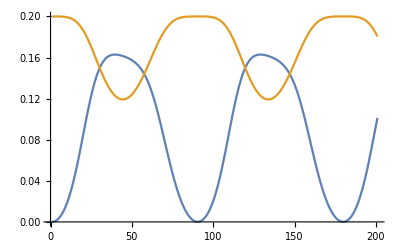

```mathematica
errorPropagation[n_,vec_,vecError_,rx_,ry_,rz_]:=(
(*v=NestList[N[rotateVector[#,rx,ry,rz]]&,vec,n];
vErr=NestList[N[rotateVector[#,rx,ry,rz]]&,vecError,n];*)
v=NestList[rotateVector[#,rx,ry,rz]&,N@vec,n];
vErr=NestList[rotateVector[#,rx,ry,rz]&,N@vecError,n];
spherical=Map[ToSphericalCoordinates,v];
sphericalErr=Map[ToSphericalCoordinates,vErr];
{MapThread[subtractAngles,{sphericalErr[[All,3]],spherical[[All,3]]}],MapThread[subtractAngles,{sphericalErr[[All,2]],spherical[[All,2]]}]}
);

ListLinePlot[errorPropagation[200,{1,0,0},N[rotateVector[{1,0,0},0,0.2,0]],Pi/100,Pi/100,Pi/100]]
```

```mathematica
(*Plot[subtractAngles[
ToSphericalCoordinates[N[rotateVector[N[rotateVector[{1,0,0},0,0.2,0]],n*Pi/100,n*Pi/100,n*Pi/100]]][[2]],
ToSphericalCoordinates[N[rotateVector[{1,0,0},n*Pi/100,n*Pi/100,n*Pi/100]]][[2]]],
{n,0,200}]*)
```